```mathematica
diffPD1 = {cA''[x]== ((phiA^2)/(L^2))*cA[x],cA'[0]==0, cA[L]==a};
solPD1 = DSolve[diffPD1, cA[x],x]
```

{{cA[x]→(a ⅇ^(phiA-(phiA x)/L) (1+ⅇ^((2 phiA x)/L)))/(1+ⅇ^(2 phiA))}}

```mathematica
Sim = FullSimplify[solPD1]
```

{{cA[x]→a Cosh[(phiA x)/L] Sech[phiA]}}

```mathematica
diffPD2 = {cB''[x]==((+phiB^2)/(L^2))*cB[x]+ ((-phiA^2)/(L^2))*a*Cosh[(phiA x)/L]*Sech[phiA],cB'[0]==0, cB[L]==0}
solPD2= DSolve[diffPD2, cB[x],x]
```

{cB''[x]==26315.8 cB[x]-10389.3 Cosh[324.443 x],cB'[0]==0,cB[0.0005]==0}

{{cB[x]→0.066448 ⅇ^(-162.221 x) (1.+1. ⅇ^(324.443 x)-1.98047 ⅇ^(162.221 x) Cosh[324.443 x])}}

```mathematica
SimPD2 = FullSimplify[solPD2]
```

{{cB[x]→0.132896 Cosh[162.221 x]-0.131598 Cosh[324.443 x]}}

```mathematica
diffPD3 = {cA''[u]== (phiA^2)*cA[u],cA'[0]==0, cA[1]==a};
solPD3 = DSolve[diffPD3, cA[u],u]
```

{{cA[u]→(a ⅇ^(phiA-phiA u) (1+ⅇ^(2 phiA u)))/(1+ⅇ^(2 phiA))}}

```mathematica
Sim3 = FullSimplify[solPD3]
```

{{cA[u]→a Cosh[phiA u] Sech[phiA]}}

```mathematica
diffPD4 = {cB''[u]==(phiB^2)*cB[u]+ (-phiA^2)*a*Cosh[phiA*u]*Sech[phiA],cB'[0]==0, cB[1]==0}
solPD4= DSolve[diffPD4, cB[u],u]
```

{cB''[u]==phiB^2 cB[u]-a phiA^2 Cosh[phiA u] Sech[phiA],cB'[0]==0,cB[1]==0}

{{cB[u]→-(a ⅇ^(-phiB u) phiA^2 (ⅇ^phiB+ⅇ^(phiB+2 phiB u)-ⅇ^(phiB u) Cosh[phiA u] Sech[phiA]-ⅇ^(2 phiB+phiB u) Cosh[phiA u] Sech[phiA]))/((1+ⅇ^(2 phiB)) (-phiA+phiB) (phiA+phiB))}}

```mathematica
Sim4 =  FullSimplify[solPD4]
```

{{cB[u]→(a phiA^2 (-Cosh[phiA u] Sech[phiA]+Cosh[phiB u] Sech[phiB]))/(phiA^2-phiB^2)}}

```mathematica
L=0.05;
```

```mathematica
kA= 2;
kB = 0.5;
a =0.1;
Deff= 1.9*10^(-5);
```

```mathematica
phiA=L*(kA/Deff)^0.5;
phiB=L*(kB/Deff)^0.5;
```

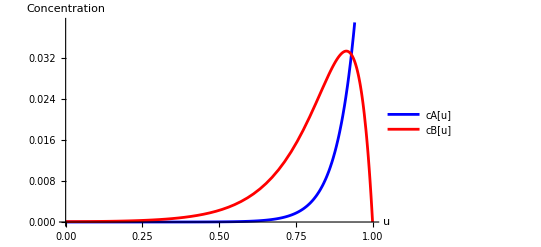

```mathematica
Plot[{Evaluate[cA[u]/. Sim3[[1]]],Evaluate[cB[u]/. Sim4[[1]]]},{u,0,1},PlotLegends->{"cA[u]","cB[u]"},AxesLabel->{"u","Concentration"},PlotStyle->{Blue,Red}]
```

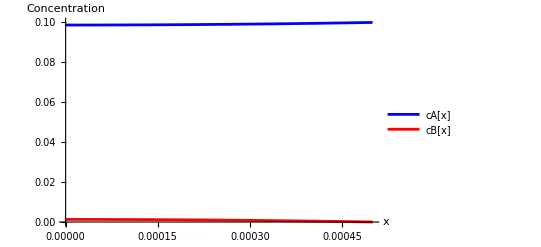

```mathematica
Plot[{Evaluate[cA[x]/. solPD1[[1]]],Evaluate[cB[x]/. SimPD2[[1]]]},{x,0.00000001,L},PlotLegends->{"cA[x]","cB[x]"},AxesLabel->{"x","Concentration"},PlotStyle->{Blue,Red}]
```

```mathematica
Exit[]
```

```mathematica
ClearAll
```

ClearAll